```mathematica
ClearAll["Global`*"];
```

```mathematica
Δs1=√(c^2×Δt1^2-Δx1^2);
Δs2=√(c^2×Δt2^2-Δx2^2);
```

```mathematica
Δx1=0k
```

0

```mathematica
Δt1=10;
```

```mathematica
c=3×10^8;
```

```mathematica
r1=Solve[Δs1==Δs2,Δx2];
```

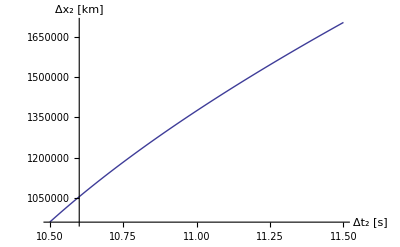

```mathematica
Plot[Δx2×10^-3/.r1[[2,1]],{Δt2,10.5,11.5},
AxesLabel->{"Δt_2 [s]","Δx_2  [km]"}]
```

```mathematica
r2=Solve[Δt2==Δt1/(√(1-v^2/c^2)),v]
```

{{v→-(300000000 √(-100+Δt2^2))/Δt2},{v→(300000000 √(-100+Δt2^2))/Δt2}}

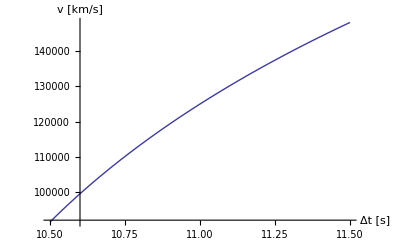

```mathematica
Plot[v * 10^-3/.r2[[2,1]],{Δt2,10.5,11.5},
AxesLabel->{"Δt [s]","v  [km/s]"}]
```